```mathematica
ω=.
i=.
x=.
n=.
h=.
```

```mathematica
(* EQ 15 *)
gxib=Exp[∑_(i=1)^n β[[i]] x[[i]]];//Quiet
```

```mathematica
(* EQ 19 *)
pixiG=(1-(1-h)^(gxib)) ∏_(k=1)^(i-1) ((1-h)^(gxib));
```

```mathematica
(* EQ 32 *)
lnL=-ω ∑_(i=1)^n ((1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6]Exp[x7[[i]] β7]Exp[x8[[i]] β8] Exp[x9[[i]] β9] Exp[x10[[i]] β10])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5]Exp[x6[[k]] β6]Exp[x7[[k]] β7]Exp[x8[[k]] β8] Exp[x9[[k]] β9] Exp[x10[[k]] β10])))+Log[ω]∑_(i=1)^n (y[[i]] ) + ∑_(i=1)^n (y[[i]] Log[(1-(1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6]Exp[x7[[i]] β7]Exp[x8[[i]] β8] Exp[x9[[i]] β9] Exp[x10[[i]] β10])) ∏_(k=1)^(i-1) ((1-h)^(Exp[x1[[k]] β1]Exp[x2[[k]] β2]Exp[x3[[k]] β3] Exp[x4[[k]] β4] Exp[x5[[k]] β5]Exp[x6[[k]] β6]Exp[x7[[k]] β7]Exp[x8[[k]] β8] Exp[x9[[k]] β9] Exp[x10[[k]] β10]))])-∑_(i=1)^n Log[y[[i]]!];//Quiet
```

```mathematica
(* Hazard Functions *)
GM=b;
NB2=(i b^2)/(1+b (i-1));
DW2=1-b^(i^2-(i-1)^2);
DW3=1-Exp[-c i^b];
S=p (1-pi^i);
TL=(1-Exp[-1/d])/(1+Exp[-(i-c)/d]);
IFRSB=1-c/i;
IFRGSB=1-c/((i-1) α+1);
```

```mathematica
(* Covariate data *)
Cov1={0.0531,0.0619,0.158,0.081,1.046,1.75,2.96,4.97,0.42,4.7,0.9,1.5,2,1.2,1.2,2.2,7.6};
Cov2={4,20,1,1,32,32,24,24,24,30,0,8,8,12,20,32,24};
Cov3={1,0,0.5,0.5,2,5,4.5,2.5,4,2,0,4,6,4,6,10,8};
Cov4=RandomReal[{1,2}] Cov1
Cov5=RandomReal[] Cov2
Cov6=RandomReal[] Cov3
Cov7=RandomReal[{1,2}] Cov1
Cov8=RandomReal[] Cov2
Cov9=RandomReal[] Cov3
Cov10=RandomReal[] Cov2
```

{0.0686676,0.0800475,0.204322,0.104747,1.35266,2.26306,3.8278,6.42708,0.543133,6.07792,1.16386,1.93976,2.58635,1.55181,1.55181,2.84498,9.82813}

{1.50784,7.53918,0.376959,0.376959,12.0627,12.0627,9.04702,9.04702,9.04702,11.3088,0.,3.01567,3.01567,4.52351,7.53918,12.0627,9.04702}

{0.550577,0.,0.275288,0.275288,1.10115,2.75288,2.4776,1.37644,2.20231,1.10115,0.,2.20231,3.30346,2.20231,3.30346,5.50577,4.40462}

{0.0546292,0.0636826,0.16255,0.0833327,1.07612,1.8004,3.04524,5.11313,0.432095,4.83535,0.925919,1.5432,2.0576,1.23456,1.23456,2.26336,7.81887}

{0.381582,1.90791,0.0953956,0.0953956,3.05266,3.05266,2.28949,2.28949,2.28949,2.86187,0.,0.763165,0.763165,1.14475,1.90791,3.05266,2.28949}

{0.853784,0.,0.426892,0.426892,1.70757,4.26892,3.84203,2.13446,3.41514,1.70757,0.,3.41514,5.12271,3.41514,5.12271,8.53784,6.83028}

{0.42108,2.1054,0.10527,0.10527,3.36864,3.36864,2.52648,2.52648,2.52648,3.1581,0.,0.842161,0.842161,1.26324,2.1054,3.36864,2.52648}

```mathematica
(* Loop to generate failure counts *)
ω=55;
FC=List[];
For[j=1,j≤17,j++,
i=j;
x={Cov1[[j]],Cov2[[j]],Cov3[[j]],Cov4[[j]],Cov5[[j]],Cov6[[j]],Cov7[[j]],Cov8[[j]],Cov9[[j]],Cov10[[j]]};
FC=Append[FC,Part[RandomVariate[PoissonDistribution[ω pixiG/.{n->10,β->{0.21774224,0.03132722,0.17702043,0.01,0.01,0.01,0.01,0.01,0.01,0.01},h->GM/.{b->0.026192}}],1],1]];//Quiet
]
ω=.
FC
n=Length[FC]
```

{2,2,3,2,6,1,2,1,2,1,1,1,1,1,0,0,0}

17

```mathematica
(* Cummulative Failure Count *)
CummulativeFC = List[FC[[1]]];
For[j=2,j≤17,j++,
CummulativeFC=Append[CummulativeFC,FC[[j]]+CummulativeFC[[j-1]]];
]
CummulativeFC
```

{2,4,7,9,15,16,18,19,21,22,23,24,25,26,26,26,26}

```mathematica
(* MLEs *)
h=GM;
lnLa=lnL/.{y-> FC,x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5,x6->Cov6,x7->Cov7,x8->Cov8,x9->Cov9,x10->Cov10};//Quiet
Rules=FindRoot[{{0==D[lnLa,ω]},{0==D[lnLa,β1]},{0==D[lnLa,β2]},{0==D[lnLa,β3]},{0==D[lnLa,β4]},{0==D[lnLa,β5]},{0==D[lnLa,β6]},{0==D[lnLa,β7]},{0==D[lnLa,β8]},{0==D[lnLa,β9]},{0==D[lnLa,β10]},{0==D[lnLa,b]}},{{ω,55},{β1,0.217},{β2,0.0313},{β3,0.177},{β4,0.01},{β5,0.01},{β6,0.217},{β7,0.0313},{β8,0.177},{β9,0.01},{β10,0.01},{b,0.0261}},MaxIterations->100000]
```

{ω→53.5347,β1→-0.206373,β2→0.0108958,β3→-0.293802,β4→0.01,β5→0.0110017,β6→0.217,β7→0.0313,β8→0.177,β9→0.01,β10→0.01,b→0.0456961}

```mathematica
(* Model fit *)
j=.
Hω=∑_(i=1)^j ω(1-((1-h)^(Exp[x1[[i]] β1]Exp[x2[[i]] β2]Exp[x3[[i]] β3] Exp[x4[[i]] β4] Exp[x5[[i]] β5]Exp[x6[[i]] β6]Exp[x7[[i]] β7]Exp[x8[[i]] β8] Exp[x9[[i]] β9] Exp[x10[[i]] β10]))) ∏_(g=1)^(i-1) (1-h)^(Exp[x1[[g]] β1]Exp[x2[[g]] β2]Exp[x3[[g]] β3] Exp[x4[[g]] β4] Exp[x5[[g]] β5]Exp[x6[[g]] β6]Exp[x7[[g]] β7]Exp[x8[[g]] β8] Exp[x9[[g]] β9] Exp[x10[[g]] β10])/.Rules/.{x1->Cov1,x2->Cov2,x3->Cov3,x4->Cov4,x5->Cov5,x6->Cov6,x7->Cov7,x8->Cov8,x9->Cov9,x10->Cov10};//Quiet
HωList={};
For[k=1,k≤ n,
AppendTo[HωList,Hω/.j->k];
k=k+1;
];
HωList//N
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{2.34697,6.73218,8.71891,10.6446,14.001,15.7117,16.8432,17.949,19.6743,21.0775,22.3643,23.1228,23.6149,24.4846,25.2746,25.7776,26.}

```mathematica
(* Goodness of fit *)
AIC=2 p-2 lnLa/.Rules/.p-> 12
BIC=+ p Log[n]-2 lnLa/.Rules/.p-> 12
SSE=∑_(i=1)^n (HωList[[i]]-CummulativeFC[[i]])^2
```

66.1952

76.1937

25.341

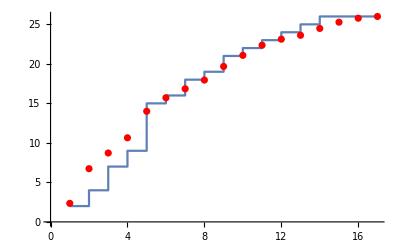

```mathematica
(* Plot data and model fit *)
gEmpirical=ListPlot[CummulativeFC,InterpolationOrder->0,Joined->True];
gFitted=ListPlot[HωList,PlotStyle->Red];(*,Joined->True,InterpolationOrder->4*)
Show[gEmpirical,gFitted]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Intervals=Table[i,{i,1,17}];
(* Good fits can't easily be achieved for high covariates, remove fitness condition for export *)
Export["GM_10cov_sim.xlsx",Transpose[{Intervals,FC,Cov1,Cov2,Cov3, Cov4, Cov5, Cov6, Cov7, Cov8, Cov9, Cov10}]]
```

GM_10cov_sim.xlsx